## Uspesnošt izobraževalnega sistema Primerjanje učinkovitosti izobraževalnega sistema v Sloveniji z drugimi državami. Pridobivanje podatkov

Podatke sem pridobil s Our World In Data.

```mathematica
GDP = Import["C:\\ROM-podatki\\GDP.csv", "Dataset", "HeaderLines"->1]
```

Dataset[<>]

```mathematica
izobrazenost = Import["C:\\ROM-podatki\\Povprecno_znanje_ucencev.csv","Dataset","HeaderLines"->1]
```

Podatki zajemajo leta od 2000 do 2024 za GDP, ter od 2010 do 2020 za znanje učencev  (Za vse države kjer so te podatki dostopni,) .

## Analiza podatkov o izobraženosti učenjakov glede na čas

Analiziral bom rezultat testov v Sloveniji in primerjavo z najboljšo državo, povprečjem, ter sosedi.

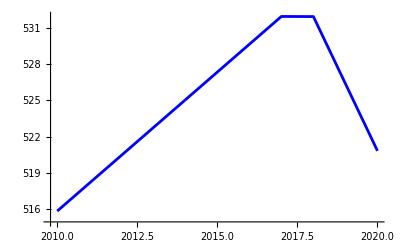

```mathematica
ListLinePlot[izobrazenost[Select[#"Entity"=="Slovenia"&],{3,4}]]
```

V grafu lahko prepoznamo, da je v okolici leta 2018 padlo znanje, kar lahko povežemo s Korona virusom.
Tedaj bom to predpostavko primerjal še z sosednjimi državami, hkrati bom tako tudi preveril na kakšnem nivoju znanja smo glede na sosede.

```mathematica
GraficniPrikazZnanja[drzava_, barva_]:=ListLinePlot[izobrazenost[Select[#"Entity"==drzava&],{3,4}], PlotStyle->barva, PlotLegends->Placed[SwatchLegend[{barva},{drzava}],Right]]
```

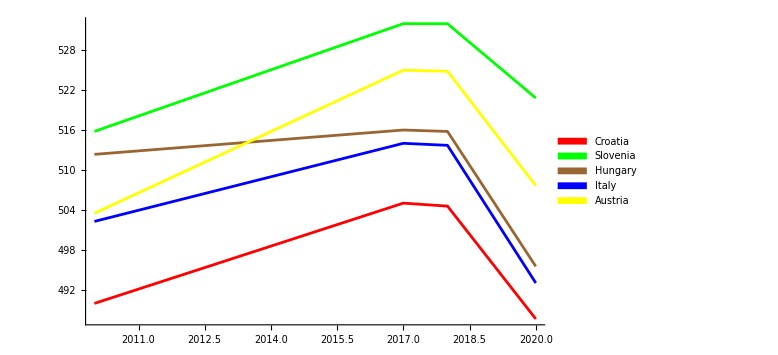

```mathematica
Show[GraficniPrikazZnanja["Croatia",Red],GraficniPrikazZnanja["Slovenia",Green],GraficniPrikazZnanja["Hungary",Brown],GraficniPrikazZnanja["Italy",Blue],GraficniPrikazZnanja["Austria", Yellow],ImageSize->Large, PlotRange->All]
```

Zelo razvidno je, da vpadlo znanje v okolici leta 2019 ni le znaminito za Slovenijo, temveč tudi njene sosede. Prav tako pa lahko vidimo, da je znanje v Sloveniji malo bolje kot znanje učencev v sosednjih državah. Pa preverimo še z državo, ki je povprečno ocenjena najbolje, ter povrprečjem.

```mathematica
drzavaNajvisjePovp=izobrazenost[MaximalBy[#"Harmonized test scores among all students"&],"Entity"][[1]]
```

Singapore

```mathematica
letnoPovp=GroupBy[izobrazenost,"Year",Mean[Select[#[[All,"Harmonized test scores among all students"]],NumberQ]]&]
```

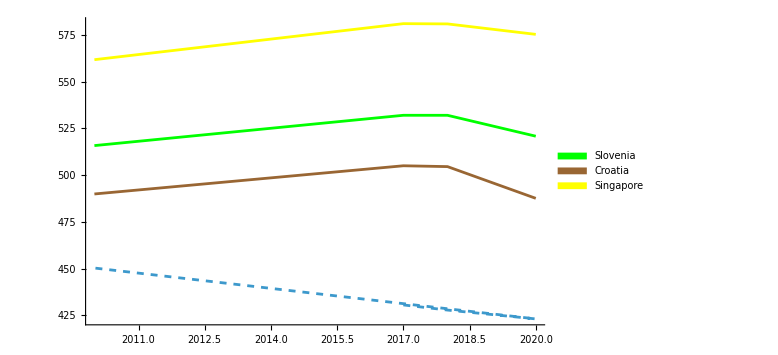

```mathematica
Show[ListLinePlot[letnoPovp,PlotStyle->Dashed,PlotLegends->"Overall Yearly Average"],GraficniPrikazZnanja["Slovenia",Green],GraficniPrikazZnanja["Croatia",Brown],GraficniPrikazZnanja[drzavaNajvisjePovp,Yellow],ImageSize->Large,PlotRange->All]
```

Razvidno je, da je slovenija, kot njene sosednje države bistveno nad povprečnim rezultatom testa.

## Analiziral bom koliko GDP je porabljenega na šolstvu v Sloveniji proti ostalim državam

Primerjal bom slovenijo proti sosednjih državam in povprečju vseh držav.

```mathematica
GraficniPrikaz[drzava_, barva_]:=ListLinePlot[GDP[Select[#"Entity"==drzava&],{3,4}], PlotStyle->barva, PlotLegends->Placed[SwatchLegend[{barva},{drzava}],Right]]
```

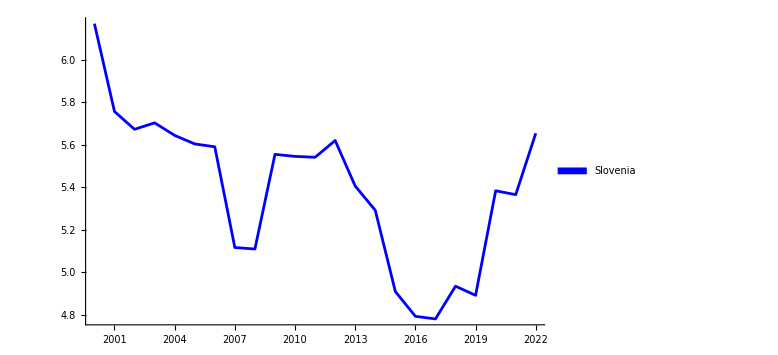

```mathematica
Show[GraficniPrikaz["Slovenia",Blue], ImageSize->Large, PlotRange->All]
```

Zanimivo je,  da v času kjer znanje pada se poveča % GDP zapravljenega na šolstvu.

```mathematica
GraficniPrikazGPD[drzava_,barva_]:=ListLinePlot[GDP[Select[#"Entity"==drzava&&2018<=#["Year"]<=2022&],{3,4}],PlotStyle->barva,PlotLegends->Placed[SwatchLegend[{barva},{drzava}],Right]]
```

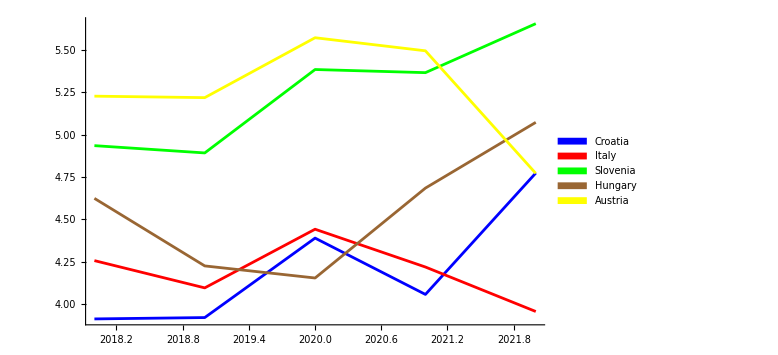

```mathematica
Show[GraficniPrikazGPD["Croatia",Blue],GraficniPrikazGPD["Italy",Red],GraficniPrikazGPD["Slovenia",Green],GraficniPrikazGPD["Hungary",Brown],GraficniPrikazGPD["Austria",Yellow],ImageSize->Large, PlotRange->All]
```

Razvidno je da ne velja enako za vse.

```mathematica
drzavaNajvisjePovp2= GDP[MaximalBy[#"Public spending on education as a share of GDP (historical and recent)"&],"Entity"][[1]]
```

Kiribati

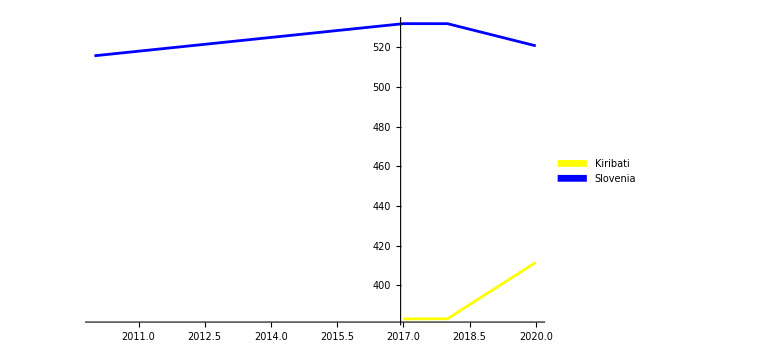

```mathematica
Show[GraficniPrikazZnanja[drzavaNajvisjePovp2, Yellow], GraficniPrikazZnanja["Slovenia", Blue], ImageSize->Large,PlotRange->All]
```

Vidimo, da se za razliko od Slovenije in sosedov pri Kiribati veča število točk tudi v okolici Korone. To pomeni da v času korone iz trenutno vidnih podatkov nemoramo povleci nobene dobre korelacije med porabo GDP, ter točkami.

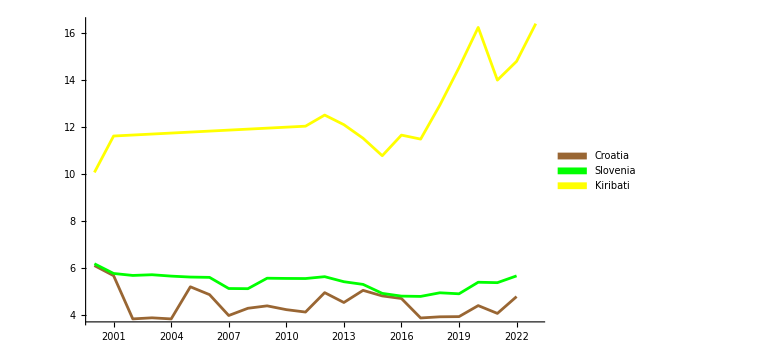

```mathematica
Show[GraficniPrikaz["Croatia",Brown],GraficniPrikaz["Slovenia",Green],GraficniPrikaz[drzavaNajvisjePovp2,Yellow],ImageSize->Large,PlotRange->All]
```

Kot razvidno čeprav slovenija porabi veliko GDP na šolstvu ni niti blizu državi, ki zapravi največ.

## Korelacija med GDP in rezultati testov

V tem poglavju bom preveril, ali obstaja korelacija med višino GDP in uspešnostjo šolskega sistema. Ugotavljal bom, ali večji finančni vložek države v izobraževanje vodi k boljšim rezultatom testov.

```mathematica
IzracunajRazmerje[dataset1_,dataset2_]:=Module[{joinedDS,filteredDS},joinedDS=JoinAcross[dataset1,dataset2,{"Entity","Year"}];
filteredDS=Select[joinedDS,NumberQ[#["Public spending on education as a share of GDP (historical and recent)"]]&&NumberQ[#["Harmonized test scores among all students"]]&];
Dataset[Map[<|"Entity"->#["Entity"],"Code"->#["Code"],"Year"->#["Year"],"Ratio"->#["Harmonized test scores among all students"]/#["Public spending on education as a share of GDP (historical and recent)"]|>&,filteredDS]]]
```

```mathematica
newDataset=IzracunajRazmerje[GDP,izobrazenost]
```

```mathematica
GraficniPrikazRazmerja[dataset_,drzava_,barva_]:=ListLinePlot[Map[{#["Year"],#["Ratio"]}&,SortBy[Select[dataset,#"Entity"==drzava&],"Year"]],PlotStyle->barva,PlotLegends->Placed[SwatchLegend[{barva},{drzava}],Right]]
```

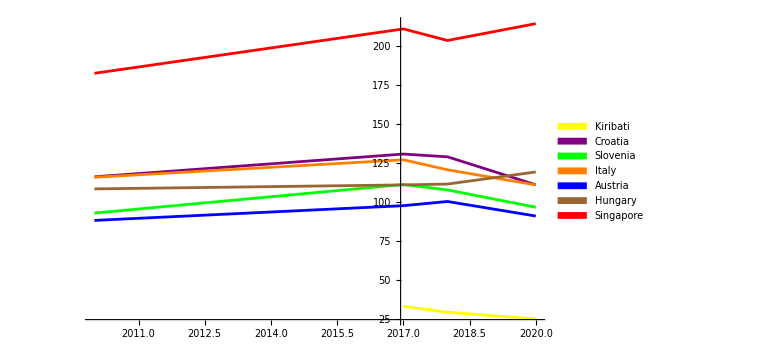

```mathematica
Show[GraficniPrikazRazmerja[newDataset,"Kiribati",Yellow],GraficniPrikazRazmerja[newDataset,"Croatia",Purple],GraficniPrikazRazmerja[newDataset,"Slovenia",Green],GraficniPrikazRazmerja[newDataset,"Italy",Orange],GraficniPrikazRazmerja[newDataset,"Austria",Blue],GraficniPrikazRazmerja[newDataset,"Hungary",Brown],GraficniPrikazRazmerja[newDataset,"Singapore",Red],ImageSize->Large,PlotRange->All]
```

V primeru Slovenije in sosednjih držav (Avstrije, Hrvaške, Madžarske in Italije) analiza kaže na pozitivno korelacijo: države, ki namenijo večji delež GDP izobraževanju, imajo praviloma višje rezultate testov. To potrjuje tudi prikazano gibanje, kjer se vse omenjene države nahajajo v podobnem razponu. Kljub temu pa analiza na širšem vzorcu (vključno s podatki za Kiribati in Singapore) razkriva, da višji GDP ne zagotavlja vedno boljših rezultatov. Ta izjema nakazuje, da je BDP pomemben dejavnik pri uspešnosti izobraževalnega sistema, vendar ni edini.

Uspešnost je verjetno odvisna tudi od drugih dejavnikov, kot so učinkovitost porabe sredstev, kakovost učiteljev in splošna organizacija izobraževalnega sistema.